```mathematica
r31 = Simplify[-c*(9*a^5*b^2+9*a^5*c^2+9*a^4*b^3+9*a^4*b*c^2+6*a^3*b^4+30*a^3*b^2*c^2+24*a^3*c^4+6*a^2*b^5+30*a^2*b^3*c^2+24*a^2*b*c^4+a*b^6+9*a*b^4*c^2+24*a*b^2*c^4+16*a*c^6+b^7+9*b^5*c^2+24*b^3*c^4+16*b*c^6)/(24*a^4*b^4-96*a^3*b^3*c^2+144*a^2*b^2*c^4-96*a*b*c^6+24*c^8)]

r21 = Simplify[(1/24)*(c^2*(3*a^3+a^2*b+3*a*c^2+b*c^2)^2+c^2*(2*a^2*b+a*b^2+a*c^2+b^3+3*b*c^2)^2-12*(a*b-c^2)^4-2*(a*b-c^2)^2*(2*c^2*(a+b)^2+(a^2+c^2)^2+(b^2+c^2)^2)+2*(a^3*b+2*a^2*c^2+3*a*b*c^2+b^2*c^2+c^4)^2)/(a*b-c^2)^4]
r11 =Simplify[(1/24)*(9*a^4*b^4+9*a^4*c^4-36*a^3*b^3*c^2+36*a^3*b*c^4+6*a^2*b^4*c^2+120*a^2*b^2*c^4+6*a^2*c^6+12*a*b^5*c^2+60*a*b^3*c^4-24*a*b*c^6+b^8+10*b^6*c^2+27*b^4*c^4+10*b^2*c^6+10*c^8)/(a^4*b^4-4*a^3*b^3*c^2+6*a^2*b^2*c^4-4*a*b*c^6+c^8)]
```

-((a+b) c (b^2+c^2) (3 a^2+b^2+4 c^2)^2)/(24 (-a b+c^2)^4)

((3 a+b)^2 c^2 (a^2+c^2)^2-12 (-a b+c^2)^4+2 (a^3 b+2 a^2 c^2+3 a b c^2+b^2 c^2+c^4)^2+c^2 (2 a^2 b+b^3+3 b c^2+a (b^2+c^2))^2-2 (-a b+c^2)^2 (2 (a+b)^2 c^2+(a^2+c^2)^2+(b^2+c^2)^2))/(24 (-a b+c^2)^4)

(b^8+10 b^6 c^2+27 b^4 c^4+10 b^2 c^6+10 c^8-36 a^3 b c^2 (b^2-c^2)+12 a b c^2 (b^4+5 b^2 c^2-2 c^4)+9 a^4 (b^4+c^4)+6 a^2 c^2 (b^4+20 b^2 c^2+c^4))/(24 (-a b+c^2)^4)

```mathematica
Eliminate[{ 0 ==  (a+b) *c* (b^2+c^2) *(3 *a^2+b^2+4 *c^2)^2, x == a^2 + c^2 , y == b^2 + c^2 , z ==c*(a+b)}, {a,b,c}]
```

9 x^2 y z+6 x y^2 z==-y^3 z

```mathematica
num3 = Factor[9 x^2 y z+6 x y^2 z+y^3 z]
```

y (3 x+y)^2 z

```mathematica
Eliminate[{0 == (3 a+b)^2 c^2 (a^2+c^2)^2-12 (-a b+c^2)^4+2 (a^3 b+2 a^2 c^2+3 a b c^2+b^2 c^2+c^4)^2+c^2 (2 a^2 b+b^3+3 b c^2+a (b^2+c^2))^2-2 (-a b+c^2)^2 (2 (a+b)^2 c^2+(a^2+c^2)^2+(b^2+c^2)^2), x == a^2 + c^2 , y == b^2 + c^2 , z ==c*(a+b)}, {a,b,c}]
```

x y (2 y^2-24 z^2)+x^2 (12 y^2-9 z^2)==z^2 (3 y^2-6 z^2)

```mathematica
num2 = Simplify[x y (2 y^2-24 z^2)+x^2 (12 y^2-9 z^2)-z^2 (3 y^2-6 z^2)]
```

-3 y^2 z^2+6 z^4+3 x^2 (4 y^2-3 z^2)+2 x (y^3-12 y z^2)

```mathematica
Eliminate[{0 == b^8+10 b^6 c^2+27 b^4 c^4+10 b^2 c^6+10 c^8-36 a^3 b c^2 (b^2-c^2)+12 a b c^2 (b^4+5 b^2 c^2-2 c^4)+9 a^4 (b^4+c^4)+6 a^2 c^2 (b^4+20 b^2 c^2+c^4), x == a^2 + c^2 , y == b^2 + c^2 , z ==c*(a+b)}, {a,b,c}]
```

-y^4-6 y^2 z^2-18 z^4==9 x^2 y^2-18 x y z^2

```mathematica
num1 = Simplify[-y^4-6 y^2 z^2-18 z^4-9 x^2 y^2+18 x y z^2]
```

-9 x^2 y^2-y^4+18 x y z^2-6 y^2 z^2-18 z^4

```mathematica
den = 24*(-x*y  + z^2)^2
```

24 (-x y+z^2)^2

```mathematica
r1 = -num1/den
r2 = -num2/den
r3 = -num3/den
```

(9 x^2 y^2+y^4-18 x y z^2+6 y^2 z^2+18 z^4)/(24 (-x y+z^2)^2)

(3 y^2 z^2-6 z^4-3 x^2 (4 y^2-3 z^2)-2 x (y^3-12 y z^2))/(24 (-x y+z^2)^2)

-(y (3 x+y)^2 z)/(24 (-x y+z^2)^2)

```mathematica
checkr1 = Simplify[ReplaceAll[ReplaceAll[ReplaceAll[r1, x -> a^2 + c^2], y -> b^2 + c^2], z -> c*(a+b)]]
checkr2 = Simplify[ReplaceAll[ReplaceAll[ReplaceAll[r2, x -> a^2 + c^2], y -> b^2 + c^2], z -> c*(a+b)]]
checkr3 = Simplify[ReplaceAll[ReplaceAll[ReplaceAll[r3, x -> a^2 + c^2], y -> b^2 + c^2], z -> c*(a+b)]]
```

(18 (a+b)^4 c^4-18 (a+b)^2 c^2 (a^2+c^2) (b^2+c^2)+6 (a+b)^2 c^2 (b^2+c^2)^2+9 (a^2+c^2)^2 (b^2+c^2)^2+(b^2+c^2)^4)/(24 (-a b+c^2)^4)

-(6 (a+b)^4 c^4-3 (a+b)^2 c^2 (b^2+c^2)^2+3 (a^2+c^2)^2 (-3 (a+b)^2 c^2+4 (b^2+c^2)^2)+2 (a^2+c^2) (-12 (a+b)^2 c^2 (b^2+c^2)+(b^2+c^2)^3))/(24 (-a b+c^2)^4)

-((a+b) c (b^2+c^2) (3 a^2+b^2+4 c^2)^2)/(24 (-a b+c^2)^4)

```mathematica
Simplify[r11 - checkr1]
Simplify[r21 - checkr2]
Simplify[r31 - checkr3]
```

0

0

0

The following is solving the case in which z = 0. This is done just to show how our method coheres with the solution we achieved by hand.

```mathematica
t1 = Simplify[ReplaceAll[r1, z-> 0]]
```

1/24 (9+y^2/x^2)

```mathematica
t2 = Simplify[ReplaceAll[r2, z -> 0]]
```

-(6 x+y)/(12 x)

```mathematica
Resolve[Exists[{x,y}, t1 - k == 0 && t2 - l == 0 && x > 0 && y > 0], Reals]
```

1/2+l<0&&-15/8+k-6 l-6 l^2==0

```mathematica
Solve[-15/8+k-6 l-6 l^2==0, k]
```

{{k→3/8 (5+16 l+16 l^2)}}

```mathematica
Resolve[Exists[{x,y}, t2/t1 - l == 0 && x > 0 && y > 0], Reals]
```

1/3 (-2-√5)≤l<0

I am below using the techniques employed in the (r1, r2, r3) case to find c where I have c as the solution to an implicit equation involving c and the ratio t2/t1. In this case, z2 = t2/t1.

```mathematica
Simplify[ReplaceAll[3/8 (5+16 l+16 l^2), l -> c2*z2]]
```

15/8+6 c2 z2+6 c2^2 z2^2

```mathematica
Reduce[c2 ==15/8+6 c2 z2+6 c2^2 z2^2  && 1/3 (-2-√5) ≤ z2 && z2 < 0, c2, Reals]
```

(z2==1/3 (-2-√5)&&c2==(3 (1-2 (-2-√5)))/(4 (-2-√5)^2)-(3 √(1-4 (-2-√5)-(-2-√5)^2))/(4 (2+√5)^2))||(1/3 (-2-√5)<z2<0&&(c2==(1-6 z2)/(12 z2^2)-1/12 √((1-12 z2-9 z2^2)/z2^4)||c2==(1-6 z2)/(12 z2^2)+1/12 √((1-12 z2-9 z2^2)/z2^4)))

In the following I am trying to solve Ric = cT with the same ratios applied from the previous theorem that solved the z = 0 case. This time I am using the same technique in that the c value is the solution to an implicit equation, but since I am using t1/t2 (which is what z1 is) I have to place my c2 and z1 in different places than before.

```mathematica
Resolve[Exists[{x,y}, t1/t2 - k == 0 && x > 0 && y > 0], Reals]
```

k≤3 (2-√5)

```mathematica
Reduce[c2*z1 == 3/8 (5+16 c2+16 c2^2) && z1 ≤ 3 (2-√5)&&  c2 < -1/2, c2, Reals]
```

(z1≤-3/4&&c2==1/12 (-6+z1)-1/12 √(-9-12 z1+z1^2))||(-3/4<z1<6-3 √5&&(c2==1/12 (-6+z1)-1/12 √(-9-12 z1+z1^2)||c2==1/12 (-6+z1)+1/12 √(-9-12 z1+z1^2)))||(z1==6-3 √5&&c2==-(√5)/4-1/12 √(-9-12 (6-3 √5)+(6-3 √5)^2))

The following is the Mathematica used to solve Ric = T. To solve this, we utilized scale invariance and set our detPhi = 1.

```mathematica
det1r1 = Simplify[ReplaceAll[ReplaceAll[1/24*Numerator[r1], z^2 -> x*y - 1], z^4 -> (x*y - 1)^2]]
```

1/24 (18-6 y^2+9 x^2 y^2+y^4+6 x y (-3+y^2))

```mathematica
det1r2 = Simplify[ReplaceAll[ReplaceAll[1/24*Numerator[r2], z^2 -> x*y - 1], z^4 -> (x*y - 1)^2]]
```

1/24 (9 x^3 y+x y (-12+y^2)-3 (2+y^2)+x^2 (-9+6 y^2))

```mathematica
Resolve[Exists[{x,y,z}, det1r1 - k == 0 && det1r2 - l ==0 && (1/24)*Numerator[r3]- m == 0 && x*y - z^2 == 1 && x > 0 && y > 0 && m>0], Reals]
(l≤-3/4&&m>0&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])||(-3/4<l≤-1/2&&((0<m<1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])||(m==1/2 √(3/2) √(3+4 l)&&k==3/4)||(m>1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])))||(-1/2<l<-1/4&&((1/4 √3 √(1+2 l)<m<1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])||(m==1/2 √(3/2) √(3+4 l)&&k==3/4)||(m>1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])))||(l==-1/4&&(((√(3/2))/4<m<(√3)/2&&k==Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1])||(m==(√3)/2&&k==3/4)||(m>(√3)/2&&k==Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1])))||(-1/4<l<0&&((1/4 √3 √(1+2 l)<m<1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])||(m==1/2 √(3/2) √(3+4 l)&&k==3/4)||(m>1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])))||(l==0&&(((√3)/4<m<3/(2 √2)&&k==Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1])||(m==3/(2 √2)&&k==3/4)||(m>3/(2 √2)&&k==Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1])))||(l>0&&((1/4 √3 √(1+2 l)<m<1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])||(m==1/2 √(3/2) √(3+4 l)&&k==3/4)||(m>1/2 √(3/2) √(3+4 l)&&k==Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1])))
```

Here we copy and paste the above solutions for k. It is organized based on the specification of the  l value.

```mathematica
fl1 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
```

Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

```mathematica
fl21 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
```

```mathematica
fl22 = 3/4
fl23 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

fl31 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
fl32 = 3/4
fl33 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

fl41= Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]
fl42 = 3/4
fl43 = Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]

fl51 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
fl52 = 3/4
fl53 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

fl61 = Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]
fl62 = 3/4
fl63 = Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]

fl71 = Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
fl72 = 3/4
fl73 =Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]
```

In the following we show that there are really only two functions describing k. The constant function at 3/4 and fl1 which we call func1 and produce the function in terms of l describing fl1. It turns out that all of these are actually the same function just defined over different regions.

```mathematica
Simplify[fl1 - fl21]
```

0

```mathematica
Simplify[fl1 - fl23]
```

0

```mathematica
Simplify[fl1 - fl31]
Simplify[fl1 - fl33]
```

0

0

```mathematica
Simplify[fl1 - fl41]
Simplify[fl1 - fl43]
```

-Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]+Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

-Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]+Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

```mathematica
Simplify[fl1 - fl51]
Simplify[fl1 - fl53]
```

0

0

```mathematica
Simplify[fl1 - fl61]
Simplify[fl1 - fl63]
```

-Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]+Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

-Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]+Root[-135-432 l-432 l^2-288 m^2-768 m^4+(432+1152 l+1152 l^2+1536 m^2+1536 l m^2) #1+(-432-768 l-768 l^2) #1^2+128 #1^3&,1]

```mathematica
Simplify[fl1 - fl71]
Simplify[fl1 - fl73]
```

0

0

```mathematica
Simplify[fl41 - fl43]
Simplify[fl41 - fl61]
Simplify[fl41 - fl63]
```

0

Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]-Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]

Root[-27-144 m^2-384 m^4+(108+576 m^2) #1-144 #1^2+64 #1^3&,1]-Root[-135-288 m^2-768 m^4+(432+1536 m^2) #1-432 #1^2+128 #1^3&,1]

```mathematica
Simplify[fl61-fl63]
```

0

```mathematica
Simplify[ReplaceAll[fl1, l-> -1/4] - fl41]
```

0

```mathematica
Simplify[ReplaceAll[fl1, l->0] - fl61]
```

0

```mathematica
func1 = FullSimplify[ToRadicals[fl1]]
```

1/8 (9+16 l+16 l^2+((1+4 l)^2 (3+4 l)^2)/(((3+16 l+16 l^2)^3-192 (3+4 l) (5+2 l (5+4 l)) m^2+1536 m^4+8 √2 √(-((1+4 l)^3-72 m^2) (3 (3+4 l)^2 m+16 m^3)^2))^(1/3))-(256 (1+l) m^2)/(((3+16 l+16 l^2)^3-192 (3+4 l) (5+2 l (5+4 l)) m^2+1536 m^4+8 √2 √(-((1+4 l)^3-72 m^2) (3 (3+4 l)^2 m+16 m^3)^2))^(1/3))+((3+16 l+16 l^2)^3-192 (3+4 l) (5+2 l (5+4 l)) m^2+1536 m^4+8 √2 √(-((1+4 l)^3-72 m^2) (3 (3+4 l)^2 m+16 m^3)^2))^(1/3))

```mathematica
FullSimplify[ReplaceAll[ReplaceAll[func1, m -> 1/2 √(3/2) √(3+4 l)], l -> 2]]
```

3/16 (103+13 √33)

Below we have the work done to solve Ric = cT

```mathematica
Resolve[Exists[{x,y,z}, r2/r1 - l ==0 && r3/r1- m == 0 && x*y - z^2 >0 && x > 0 && y > 0 && m> 0 ], Reals]
```

(m>0&&1/2 (-2+m^2)≤l<m^2)||(0<m<1/(√3)&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(0<m≤√(2/3)&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/2 (-2+m^2))||(m>√(2/3)&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(0<m≤1/(√3)&&l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])||(1/(√3)<m<Root0.625Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&(l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]||l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]))||(m==Root0.625Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])||(0<m<1/(√3)&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(1/(√3)<m<Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)||(m==Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&1/3 (-4+3 m^2)≤l<m^2)||(Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m<Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)||(m==Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]≤l<m^2)||(m>Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)||(1/(√3)<m≤Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m<Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))||(1/(√3)<m≤Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m<Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/3 (-4+3 m^2))||(m>Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(1/(√3)<m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784<m<Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤1/3 (-4+3 m^2))||(Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m≤Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959<m<Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m>Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root0.281Root[-1+12 #1^2+9 #1^4&,2]0.2805161774893976<m≤1/(√3)&&Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,2]<l<m^2)||(1/(√3)<m<√(2/3)&&(Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<1/3 (-4+3 m^2)||Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==√(2/3)&&(Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(√(2/3)<m<Root0.875Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557&&Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m==Root0.875Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root0.875Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557<m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))||(0<m≤Root0.372Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<m^2)||(Root0.372Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342<m<Root0.423Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root0.423Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root0.423Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694<m≤Root0.556Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root0.556Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006<m<Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root1.52Root[-2812500-11259427868 #1^2-6144055152 #1^4+1352551761 #1^6+692176752 #1^8+340122240 #1^10&,2]1.5200965007140295&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root0.372Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342<m≤1/(√3)&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<m^2)||(1/(√3)<m≤Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2))||(m==Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<1/3 (-4+3 m^2))||(Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))||(1/(√3)<m≤(3 √3)/5&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||((3 √3)/5<m≤Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2))||(m==Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<1/3 (-4+3 m^2))||(Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))||(1/(√3)<m≤(3 √3)/5&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||((3 √3)/5<m≤Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/3 (-4+3 m^2))||(m>Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(1/(√3)<m≤Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2))||(Root0.986Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m≤(3 √3)/5&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||((3 √3)/5<m≤Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root1.09Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(m==Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||1/3 (-4+3 m^2)<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root1.11Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(m==Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root1.13Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(Root1.17Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root1.52Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root1.52Root[-2812500-11259427868 #1^2-6144055152 #1^4+1352551761 #1^6+692176752 #1^8+340122240 #1^10&,2]1.5200965007140295&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(0<m<Root0.423Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])||(Root0.423Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694≤m<Root0.556Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root0.556Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006≤m<1/(√3)&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==1/(√3)&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<1/3 (-4+3 m^2))||(1/(√3)<m<Root0.625Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&(Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]||Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root0.625Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436≤m<Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root1.40Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784<m<Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤1/3 (-4+3 m^2))||(Root1.56Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m≤Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root2.22Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959<m<Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m>Root2.48Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])

We handle all of this by breaking it up into the 15 sections as described by the way the solution is provided in terms of intervals of m.

```mathematica
1
```

```mathematica
(m>0&&1/2 (-2+m^2)≤l<m^2)
```

```mathematica
2
```

```mathematica
0<m<1/(√3)&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||
```

```mathematica
3
```

```mathematica
(0<m≤√(2/3)&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/2 (-2+m^2))||(m>√(2/3)&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)
```

```mathematica
4
```

```mathematica
(0<m≤1/(√3)&&l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])||(1/(√3)<m<Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&(l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]||l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]))||(m==Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&l==Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])
```

```mathematica
5
```

```mathematica
(0<m<1/(√3)&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(1/(√3)<m<Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)||(m==Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&1/3 (-4+3 m^2)≤l<m^2)||(Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m<Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)||(m==Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]≤l<m^2)||(m>Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<m^2)
```

```mathematica
6
```

```mathematica
(1/(√3)<m≤Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m<Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))
```

```mathematica
7
```

```mathematica
(1/(√3)<m≤Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m<Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/3 (-4+3 m^2))||(m>Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))
```

```mathematica
8
```

```mathematica
(1/(√3)<m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784<m<Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤1/3 (-4+3 m^2))||(Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m≤Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959<m<Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m>Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])
```

```mathematica
9
```

```mathematica
(Root"0.281"Root[-1+12 #1^2+9 #1^4&,2]0.2805161774893976<m≤1/(√3)&&Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,2]<l<m^2)||(1/(√3)<m<√(2/3)&&(Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<1/3 (-4+3 m^2)||Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==√(2/3)&&(Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(√(2/3)<m<Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557&&Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m==Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557<m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))
```

```mathematica
10
```

```mathematica
(0<m≤Root"0.372"Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<m^2)||(Root"0.372"Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342<m<Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694<m≤Root"0.556"Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root"0.556"Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006<m<Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root"1.52"Root[-2812500-11259427868 #1^2-6144055152 #1^4+1352551761 #1^6+692176752 #1^8+340122240 #1^10&,2]1.5200965007140295&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])
```

```mathematica
11
```

```mathematica
(Root"0.372"Root[-1+6 #1^2+9 #1^4&,2]0.3715793151639342<m≤1/(√3)&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<m^2)||(1/(√3)<m≤Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2))||(m==Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<1/3 (-4+3 m^2))||(Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))
```

```mathematica
12
```

```mathematica
(1/(√3)<m≤(3 √3)/5&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||((3 √3)/5<m≤Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(m==Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]))||(Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784≤m<Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2))||(m==Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<1/3 (-4+3 m^2))||(Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(m≥Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l<1/3 (-4+3 m^2))
```

```mathematica
13
```

```mathematica
(1/(√3)<m≤(3 √3)/5&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||((3 √3)/5<m≤Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(m==Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&(Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<1/3 (-4+3 m^2)||1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤1/3 (-4+3 m^2))||(m>Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))
```

```mathematica
14
```

```mathematica
(1/(√3)<m≤Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887&&Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]<l<1/3 (-4+3 m^2))||(Root"0.986"Root[1-36 #1^2+36 #1^4&,4]0.9855985596534887<m≤(3 √3)/5&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||((3 √3)/5<m≤Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2)||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root"1.09"Root[-2-9 #1^2+9 #1^4&,2]1.0895798598250046<m<Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(m==Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||1/3 (-4+3 m^2)<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211<m<Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(m==Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212&&(Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]||Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]))||(Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212<m<Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<1/3 (-4+3 m^2))||(Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657<m<Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(m==Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])||(Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408<m<Root"1.52"Root[-2812500-11259427868 #1^2-6144055152 #1^4+1352551761 #1^6+692176752 #1^8+340122240 #1^10&,2]1.5200965007140295&&Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]<l<Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2])
```

```mathematica
15
```

```mathematica
(0<m<Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1])||(Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694≤m<Root"0.556"Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"0.556"Root[1-147 #1^2+423 #1^4+135 #1^6&,4]0.55618011432006≤m<1/(√3)&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==1/(√3)&&Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<1/3 (-4+3 m^2))||(1/(√3)<m<Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436&&(Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]<l<Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]||Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]))||(Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436≤m<Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784&&1/3 (-4+3 m^2)<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784<m<Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤1/3 (-4+3 m^2))||(Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678<m≤Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959&&Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]<l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(Root"2.22"Root[1-27 #1^2-657 #1^4+135 #1^6&,4]2.215201160854959<m<Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1])||(m==Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l≤Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])||(m>Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934&&Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]≤l<Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1])
```

The above 15 chunks were placed into the Step 6 using notation from the following functions that appear above (observe that only two of them are converted to a radical form as it turns out that the rest cannot be)

```mathematica
f275m1 = Root[-2-75 m^2+(6-180 m^2) #1+(180-378 m^2) #1^2+(756-324 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]
```

```mathematica
f2213m1 = Root[-2+213 m^2+5112 m^4-2160 m^6+(6-3780 m^2+5616 m^4) #1+(180-1242 m^2-648 m^4) #1^2+(756+972 m^2) #1^3+(1134-243 m^2) #1^4+486 #1^5&,1]
```

```mathematica
f4507m1 = Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]
```

Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,1]

```mathematica
f4507m2 = Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]
```

Root[4-507 m^2+(51-1404 m^2) #1+(252-1674 m^2) #1^2+(594-972 m^2) #1^3+(648-243 m^2) #1^4+243 #1^5&,2]

```mathematica
f25m1 = Root[-25 m^2+(1+60 m^2) #1+(12-126 m^2) #1^2+(54+108 m^2) #1^3+(108-81 m^2) #1^4+81 #1^5&,1]
```

```mathematica
f1168m1 = ToRadicals[Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,1]]
```

1/3 (-1-2 √(-2 √3 m-3 m^2))

```mathematica
f1168m2 = ToRadicals[Root[1-168 m^2+144 m^4+(12+144 m^2) #1+(54+216 m^2) #1^2+108 #1^3+81 #1^4&,2]]
```

1/3 (-1+2 √(-2 √3 m-3 m^2))

```mathematica
f166360m2 = Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,2]
```

```mathematica
f166360m1 = Root[16-6360 m^2+47961 m^4+(216+8478 m^2+149796 m^4) #1+(1161+54432 m^2+176094 m^4) #1^2+(3132+64476 m^2+92340 m^4) #1^3+(4374+29160 m^2+18225 m^4) #1^4+(2916+4374 m^2) #1^5+729 #1^6&,1]
```

```mathematica
f150m2 = Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,2]
```

```mathematica
f150m1 = Root[-150 m^2+75 m^4+(2-231 m^2+540 m^4) #1+(42+4806 m^2+3402 m^4) #1^2+(378+14742 m^2+8748 m^4) #1^3+(1890-6966 m^2+19683 m^4) #1^4+(5670-45927 m^2) #1^5+(10206-13122 m^2) #1^6+10206 #1^7+4374 #1^8&,1]
```

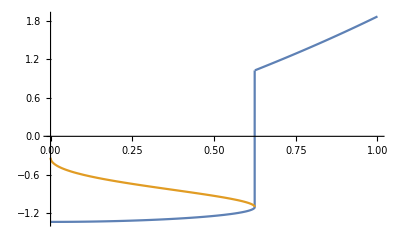

```mathematica
Plot[{f4507m1 ,f4507m2 }, {m, 0, 1}]
```

```mathematica
RootReduce[Root[4-507 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2+(51-1404 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1+(252-1674 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^2+(594-972 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^3+(648-243 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^4+243 #1^5&,2] - Root[4-507 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2+(51-1404 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1+(252-1674 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^2+(594-972 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^3+(648-243 (Root"0.625"Root[-324+692 #1^2+336 #1^4+45 #1^6&,2]0.62478314852436)^2) #1^4+243 #1^5&,1]]
```

0

```mathematica
RootReduce[Root[-2-75 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2+(6-180 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2) #1+(180-378 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2) #1^2+(756-324 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2) #1^3+(1134-243 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2) #1^4+486 #1^5&,1] - 1/3 (-4+3 (Root"1.56"Root[-18-47 #1^2+147 #1^4-117 #1^6+27 #1^8&,2]1.562285076405678)^2)]
```

0

```mathematica
RootReduce[Root[-25 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2+(1+60 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1+(12-126 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^2+(54+108 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^3+(108-81 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^4+81 #1^5&,1] - Root[-2-75 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2+(6-180 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1+(180-378 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^2+(756-324 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^3+(1134-243 (Root"2.48"Root[32768-2020986 #1^2-10826991 #1^4-2570157 #1^6-220725 #1^8+151875 #1^10&,4]2.479619861617934)^2) #1^4+486 #1^5&,1]]
```

0

```mathematica
RootReduce[Root[1-168 (Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211)^2+144 (Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211)^4+(12+144 (Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211)^2) #1+(54+216 (Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211)^2) #1^2+108 #1^3+81 #1^4&,2] -  1/3 (-4+3 (Root"1.11"Root[-27+19 #1^2-9 #1^4+9 #1^6&,2]1.1149456212916211)^2)]
```

0

```mathematica
RootReduce[Root[-25 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2+(1+60 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2) #1+(12-126 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2) #1^2+(54+108 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2) #1^3+(108-81 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2) #1^4+81 #1^5&,1] - 1/3 (-4+3 (Root"1.40"Root[-27-82 #1^2+192 #1^4-126 #1^6+27 #1^8&,2]1.4042802699723784)^2)]
```

0

```mathematica
RootReduce[ Root[16-6360 Sqrt[2/3]^2+47961 Sqrt[2/3]^4+(216+8478 Sqrt[2/3]^2+149796 Sqrt[2/3]^4) #1+(1161+54432 Sqrt[2/3]^2+176094 Sqrt[2/3]^4) #1^2+(3132+64476 Sqrt[2/3]^2+92340 Sqrt[2/3]^4) #1^3+(4374+29160 Sqrt[2/3]^2+18225 Sqrt[2/3]^4) #1^4+(2916+4374 Sqrt[2/3]^2) #1^5+729 #1^6&,2] - 1/3 (-4+3 Sqrt[2/3]^2)]
```

0

```mathematica
RootReduce[ Root[16-6360 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+47961 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4+(216+8478 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+149796(Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1+(1161+54432 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+176094 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1^2+(3132+64476 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+92340 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1^3+(4374+29160 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+18225 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1^4+(2916+4374 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2) #1^5+729 #1^6&,1] - Root[-2+213 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+5112 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4-2160 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^6+(6-3780 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2+5616 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1+(180-1242 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2-648 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^4) #1^2+(756+972 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2) #1^3+(1134-243 (Root"0.875"Root[18-965 #1^2-4029 #1^4+4293 #1^6+3375 #1^8&,4]0.8746635826537557)^2) #1^4+486 #1^5&,1]]
```

0

```mathematica
RootReduce[ Root[4-507 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2+(51-1404 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1+(252-1674 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^2+(594-972 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^3+(648-243 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^4+243 #1^5&,1] - Root[-2-75 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2+(6-180 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1+(180-378 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^2+(756-324 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^3+(1134-243 (Root"0.423"Root[32768-1855650 #1^2+10014057 #1^4-3642597 #1^6-204525 #1^8+151875 #1^10&,4]0.42274512026437694)^2) #1^4+486 #1^5&,1]]
```

0

```mathematica
RootReduce[Root[-150 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2+75 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^4+(2-231 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2+540 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^4) #1+(42+4806 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2+3402 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^4) #1^2+(378+14742 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2+8748 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^4) #1^3+(1890-6966 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2+19683 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^4) #1^4+(5670-45927 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2) #1^5+(10206-13122 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2) #1^6+10206 #1^7+4374 #1^8&,2] -  1/3 (-4+3 (Root"1.17"Root[-486-9 #1^2+3053 #1^4-4914 #1^6+3096 #1^8-837 #1^10+81 #1^12&,2]1.1744399508974657)^2)]
```

0

```mathematica
RootReduce[Root[-2+213 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+5112 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4-2160 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^6+(6-3780 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+5616 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1+(180-1242 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2-648 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1^2+(756+972 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2) #1^3+(1134-243 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2) #1^4+486 #1^5&,1] - Root[-150 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+75 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4+(2-231 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+540 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1+(42+4806 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+3402 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1^2+(378+14742 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+8748 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1^3+(1890-6966 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2+19683 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^4) #1^4+(5670-45927 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2) #1^5+(10206-13122 (Root"1.52"Root[686-49551 #1^2-203679 #1^4-60129 #1^6+68445 #1^8&,4]1.5182156907253408)^2) #1^6+10206 #1^7+4374 #1^8&,1]]
```

0

```mathematica
RootReduce[Root[1-168 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+144 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4+(12+144 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1+(54+216 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1^2+108 #1^3+81 #1^4&,2]-Root[-150 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+75 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4+(2-231 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+540 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1+(42+4806 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+3402 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^2+(378+14742 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+8748 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^3+(1890-6966 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+19683 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^4+(5670-45927 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1^5+(10206-13122 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1^6+10206 #1^7+4374 #1^8&,1]]
```

0

```mathematica
RootReduce[Root[4-507 Sqrt[1/3]^2+(51-1404 Sqrt[1/3]^2) #1+(252-1674 Sqrt[1/3]^2) #1^2+(594-972 Sqrt[1/3]^2) #1^3+(648-243 Sqrt[1/3]^2) #1^4+243 #1^5&,2] - 1/3 (-4+3 Sqrt[1/3]^2)]
```

0

```mathematica
N[Root[-150 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+75 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4+(2-231 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+540 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1+(42+4806 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+3402 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^2+(378+14742 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+8748 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^3+(1890-6966 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2+19683 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^4) #1^4+(5670-45927 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1^5+(10206-13122 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2) #1^6+10206 #1^7+4374 #1^8&,2] -  1/3 (-4+3 (Root"1.13"Root[17179869184-758241767424 #1^2+738811183104 #1^4-1873773558144 #1^6+2178248345280 #1^8+730684767357 #1^10-1168450231581 #1^12-312846367473 #1^14+307409258025 #1^16&,4]1.1301404036952212)^2)]
```

0.109102